# Scattering Kernels in Flatland

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2019 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Henyey Greenstein Generalization

[Davis 2006]

```mathematica
pHGFlatland[u_,g_]:=1/(2Pi)(1-g^2)/(1+g^2-2 g u)
```

```mathematica
Integrate[Cos[t]pHGFlatland[Cos[t],g],{t,-Pi,Pi},Assumptions->-1<g<1]
```

ConditionalExpression[g,g≠0]

```mathematica
sampleHGFlatland[g_]:=2 ArcTan[(1-g)/(1+g)Tan[Pi/2(1-2 RandomReal[])]]
```

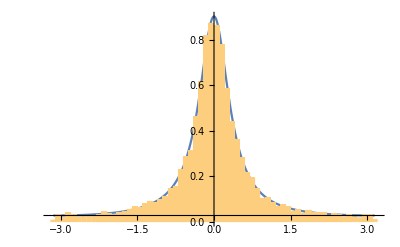

```mathematica
With[{g=0.7},
Show[
Plot[pHGFlatland[Cos[t],g],{t,-Pi,Pi},PlotRange->All],
Histogram[
Table[sampleHGFlatland[g],{i,Range[10000]}]
,50,"PDF"]
]
]
```